```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]]

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2Mm)/(hbar)^2;
Print[1/mh2]
```

{{0.5,-16.3721,4.436,0.,0.},{0.75,-28.6714,12.936,0.,0.},{1,-44.4515,27.245,0.,0.},{1.5,-86.4495,79.22,0.,0.},{2,-142.363,173.925,-117.89,33.9971},{3,-295.93,558.493,-259.85,180.091},{4,-505.15,1395.63,-457.74,488.075},{6,-1090.55,6293.03,-1020.58,1915.88},{8,-1898.55,23937.6,-1806.42,5323.05},{10,-2929.17,85318.8,-2815.55,12777.1}}

20.7369

```mathematica
I1[lam_,b1_,b2_] :=(Pi/(2b1+2b2+lam^2))^(3/2);
I2[lam_,b1_,b2_] := 0;
I3[b1_,b2_] :=3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2));
```

```mathematica
ham[lam_,b1_,b2_,scaleFac_]:=Module[{locall=lam},
LECc=scaleFac Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
 LECc I1[lam,b1,b2]+LECd I2[lam,b1,b2]+(1/mh2)I3[b1,b2]
]  ;
norm[b1_,b2_]:=Module[{},(Pi/(2b1+2b2))^(3/2)
]  ;
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

```mathematica
dimD=3;
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];

(*widths=RandomReal[{0.1,0.5},dimD];*)

lamd=6;
scaleFactor=1.0;
LECc = Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]];
Print["λ = ",lamd,"   C_0(λ) = ",LECc]

(*widths =N@logspace[dimD-1,0.05,50.04]*)
widthL=Sort[#]&/@RandomReal[{0.05,26},{13000,dimD}];
(*widthL={{0.0354,0.3549487286919056,3.5589999999999993}};*)
results=0.0;
optSet={};

Do[
dimD=Length[widths];
hamm=Table[ham[lamd,widths[[i]],widths[[j]],scaleFactor],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[eval];
eigsorted=eval[[ord]];
vecsorted=evec[[ord]];

If[((eigsorted[[1]]<results)&&(eigsorted[[1]]>-20)&&(Im[eigsorted[[1]]]==0)),
Print[eigsorted[[1]],eigsorted];
e0=eigsorted[[1]];
Print[Transpose[{vecsorted[[1]],widths}]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],widths}];
]
,{widths,widthL}]
Print["E_0 = ",e0];
Print["opt. basis: ",optSet];
Put[optSet,"tmp.lst"];
Put[e0,"E0tmp.lst"];
```

λ = 6   C_0(λ) = -1090.55

-1.46679{-1.46679,32.7059,458.255}

{{0.141828,0.150673},{0.421303,1.46507},{0.895762,10.6456}}

E_0 = -1.46679

opt. basis: {{0.141828,0.150673},{0.421303,1.46507},{0.895762,10.6456}}

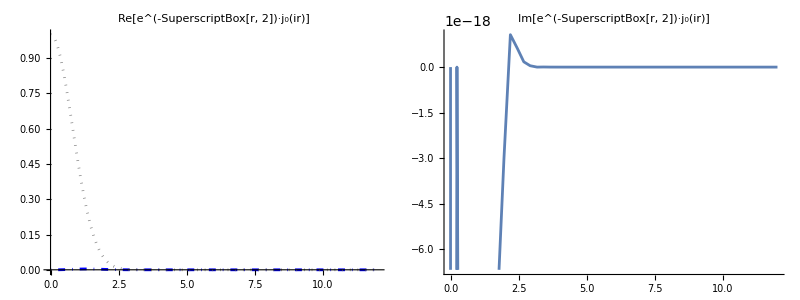

```mathematica
α=0.9;
rma=12;rmi=0.;
Grid[{{Plot[{√(π/(2  α r))BesselI[3.5,α r] Exp[-α r^2],Re[Exp[-α r^2] SphericalBesselJ[0,I α r]]},{r,rmi,rma},PlotLabel->"Re[e^(-SuperscriptBox[r, 2])·j_0(ir)]",ImageSize->Large,PlotRange->Full,PlotStyle->{Directive[Blue,DotDashed],Directive[Gray,Dotted]}],Plot[Im[Exp[-r^2] SphericalBesselJ[0,I r]],{r,rmi,rma},PlotLabel->"Im[e^(-SuperscriptBox[r, 2])·j_0(ir)]",ImageSize->Large]}}]
```

```mathematica
Max[10^-10,α 0]
```

1/10000000000